```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=8.6173324*10^-3;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/4801Ang"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesEinsteinPot={"C_3200K_energy_displacement","C_3200K_energy_displacement_harmonic","Zr_3200K_energy_displacement","Zr_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
cPlotData=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot[CarbonPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[CarbonPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
ZirconPotentialEinstein=ReadList[filesEinsteinPot[[3]],{Number, Number}];
zPlotData=ReadList[filesEinsteinPot[[3]],{Number, Number}];
ZirconPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[4]],{Number, Number}];
Show@ListPlot[ZirconPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[ZirconPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
```

```mathematica
CarbonPotentialEinsteinHarmonic
```

{{-0.0098,0.48},{0,0},{0,0},{0.0098,0.48}}

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]
V[1,4,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4},x]
V[1,6,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]
V[1,8,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[1,10,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[1,12,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
(*Zirconium*)
V[2,2,x_]:=Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]
V[2,4,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4},x]
V[2,6,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]
V[2,8,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[2,10,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[2,12,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
```

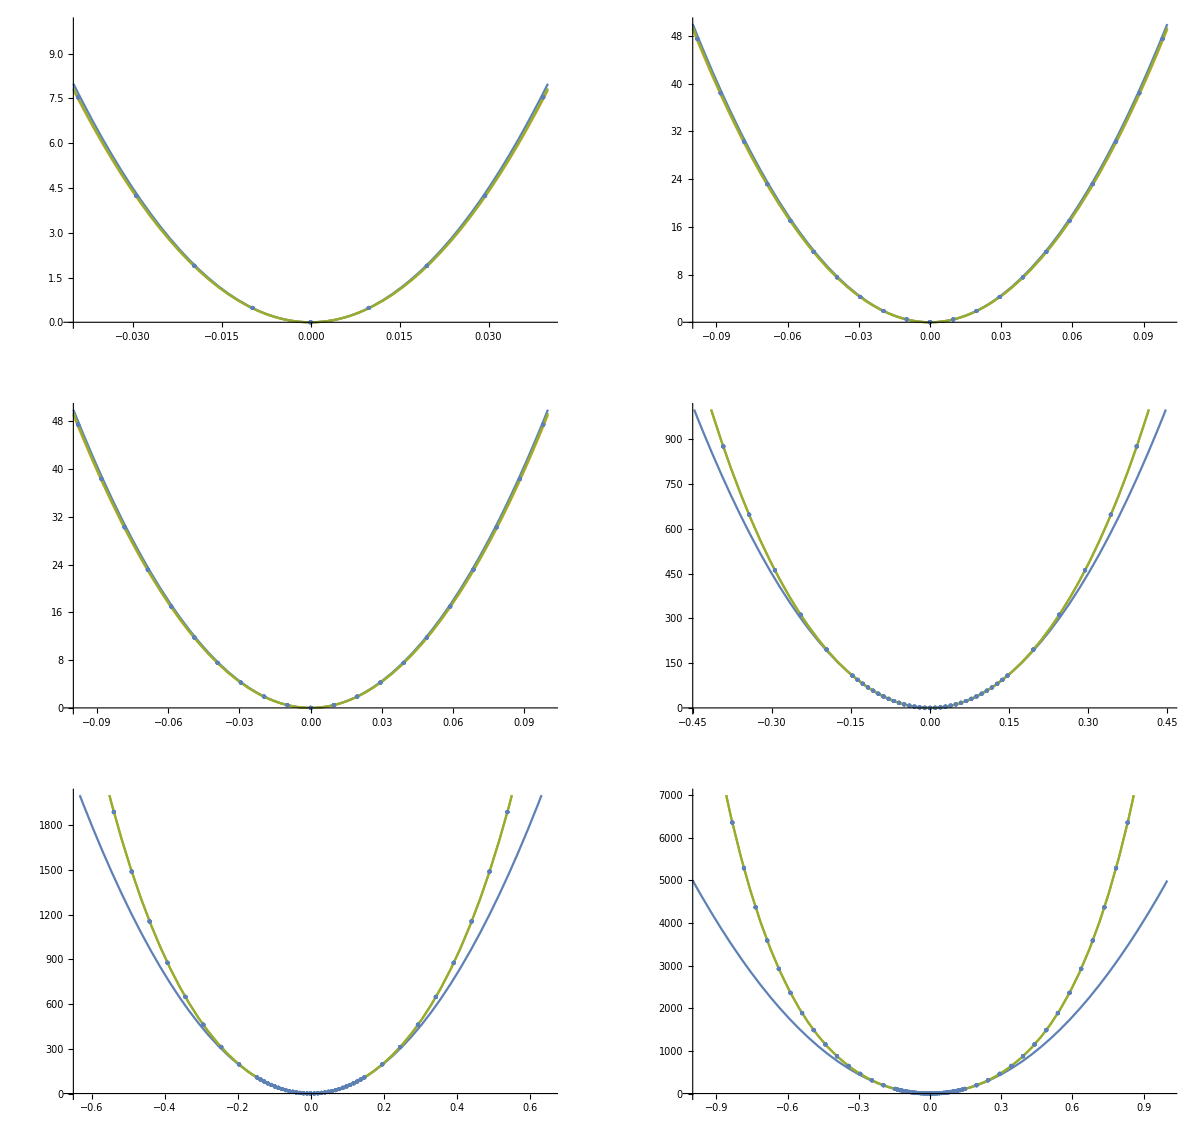

```mathematica
Carbon- look at the fits to examine agreement different length scales;
commonplotinfo={AxesLabel->{"Displacement (Å)","E-E0ref (meV) "}};
P00=With[{B=0.04,H=10},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2=With[{B=0.45,H=1000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3=With[{B=0.65,H=2000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4=With[{B=1,H=7000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00,ListPlot@cPlotData],Show[P0,ListPlot@cPlotData]},{Show[P1,ListPlot@cPlotData],Show[P2,ListPlot@cPlotData]},{Show[P3,ListPlot@cPlotData],Show[P4,ListPlot@cPlotData]}},ImageSize->1200]
```

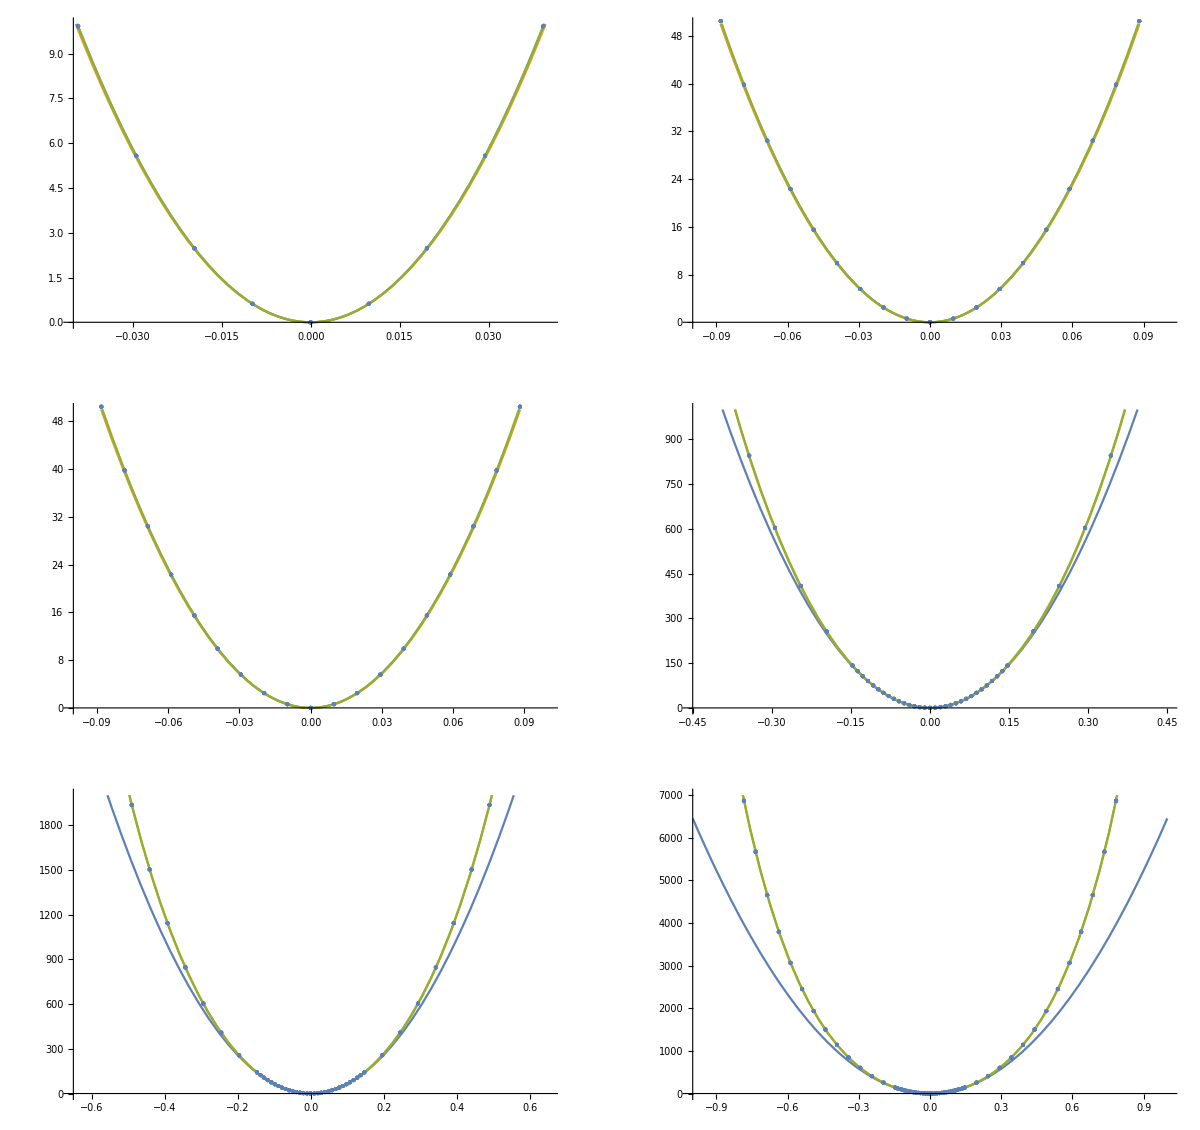

```mathematica
Look at fits at different scales - Zirconium;
P00z=With[{B=0.04,H=10},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2z=With[{B=0.45,H=1000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3z=With[{B=0.65,H=2000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4z=With[{B=1,H=7000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00z,ListPlot@zPlotData],Show[P0z,ListPlot@zPlotData]},{Show[P1z,ListPlot@zPlotData],Show[P2z,ListPlot@zPlotData]},{Show[P3z,ListPlot@zPlotData],Show[P4z,ListPlot@zPlotData]}},ImageSize->1200]
```

```mathematica
Carbon and zirconium - calculate harmonic frequency of fit (as root of prefactor *2 over mass);
(*If the fitted carbon potential is f(x)=A*x*x, let it be equal to standard harmonic expression, f(x)=A*x*x=1/2*m*omega*omega*x*x*)
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=V[1,2,x][[1]]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=V[2,2,x][[1]]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

4997.92

cOmega0 in meV/Ang**2/AMU is approximately

28.8486

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

6455.64

Z_Omega_0 in meV/Ang**2/AMU is approximately

11.8968

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first 70 eigenvalues and eigenvectors*)
Neigenvalues=70;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒall=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x],{i,2,12,2}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x],{i,2,12,2}];
(*Carbon eigensystem*)
eigensysC=Table[NDEigensystem[ℒall[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
(*Zironcium eigensystem*)
eigensysZ=Table[NDEigensystem[ℒallz[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
```

```mathematica
(*Carbon and Zironcium eigenenergies*)
(*Indexed like 1 is harmonic, 2 is 4th order ... 6 is 12th order*)
eigenEnergies=Table[eigensysC[[k]][[1]]/cOmega0,{k,1,6}];
eigenEnergiesZ=Table[eigensysZ[[k]][[1]]/zOmega0,{k,1,6}];

relativeEigenval=Table[eigensysC[[k]][[1]]/eigensysC[[1]][[1]],{k,1,6}];
relativeEigenvalz=Table[eigensysZ[[k]][[1]]/eigensysZ[[1]][[1]],{k,1,6}];
```

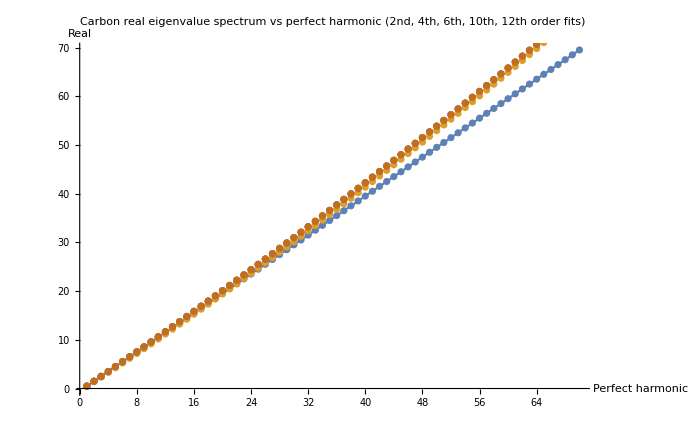

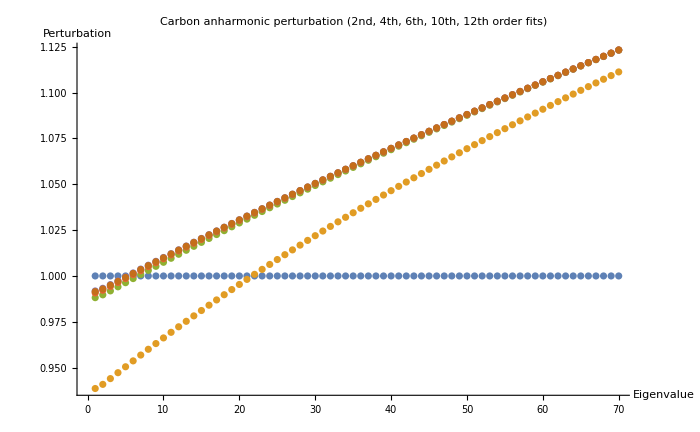

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5 | 68.5 | 69.5
0.469309 | 1.41132 | 2.36005 | 3.31536 | 4.27714 | 5.24527 | 6.21962 | 7.2001 | 8.1866 | 9.17901 | 10.1773 | 11.1812 | 12.1909 | 13.2061 | 14.2267 | 15.2528 | 16.2842 | 17.3209 | 18.3627 | 19.4097 | 20.4617 | 21.5188 | 22.5807 | 23.6475 | 24.7192 | 25.7956 | 26.8767 | 27.9624 | 29.0528 | 30.1477 | 31.2471 | 32.3509 | 33.4592 | 34.5719 | 35.6888 | 36.81 | 37.9355 | 39.0652 | 40.199 | 41.337 | 42.479 | 43.6251 | 44.7752 | 45.9293 | 47.0873 | 48.2492 | 49.415 | 50.5846 | 51.7581 | 52.9353 | 54.1163 | 55.301 | 56.4894 | 57.6815 | 58.8772 | 60.0765 | 61.2794 | 62.4859 | 63.6959 | 64.9094 | 66.1264 | 67.3468 | 68.5707 | 69.7979 | 71.0286 | 72.2627 | 73.5 | 74.7407 | 75.9847 | 77.232
0.494081 | 1.48456 | 2.47964 | 3.47929 | 4.48347 | 5.49212 | 6.50522 | 7.52273 | 8.54461 | 9.57082 | 10.6013 | 11.6361 | 12.6751 | 13.7183 | 14.7656 | 15.8171 | 16.8727 | 17.9323 | 18.996 | 20.0637 | 21.1354 | 22.2111 | 23.2906 | 24.3741 | 25.4614 | 26.5526 | 27.6477 | 28.7465 | 29.8491 | 30.9554 | 32.0655 | 33.1792 | 34.2967 | 35.4178 | 36.5426 | 37.6709 | 38.8029 | 39.9384 | 41.0775 | 42.2202 | 43.3663 | 44.516 | 45.6691 | 46.8256 | 47.9857 | 49.1491 | 50.3159 | 51.4862 | 52.6598 | 53.8367 | 55.017 | 56.2006 | 57.3875 | 58.5777 | 59.7712 | 60.9679 | 62.1678 | 63.371 | 64.5774 | 65.787 | 66.9997 | 68.2157 | 69.4347 | 70.657 | 71.8823 | 73.1107 | 74.3423 | 75.5769 | 76.8146 | 78.0554
0.495375 | 1.48835 | 2.48577 | 3.48759 | 4.49378 | 5.50432 | 6.51915 | 7.53827 | 8.56162 | 9.58919 | 10.6209 | 11.6568 | 12.6969 | 13.741 | 14.7892 | 15.8415 | 16.8977 | 17.958 | 19.0222 | 20.0903 | 21.1624 | 22.2384 | 23.3182 | 24.4018 | 25.4893 | 26.5806 | 27.6757 | 28.7745 | 29.877 | 30.9833 | 32.0932 | 33.2068 | 34.3241 | 35.445 | 36.5695 | 37.6975 | 38.8292 | 39.9644 | 41.1031 | 42.2454 | 43.3911 | 44.5403 | 45.693 | 46.8491 | 48.0087 | 49.1716 | 50.338 | 51.5077 | 52.6808 | 53.8572 | 55.0369 | 56.22 | 57.4064 | 58.596 | 59.7889 | 60.9851 | 62.1845 | 63.3871 | 64.5929 | 65.8019 | 67.0141 | 68.2295 | 69.448 | 70.6697 | 71.8945 | 73.1224 | 74.3534 | 75.5874 | 76.8246 | 78.0648
0.495904 | 1.48989 | 2.48821 | 3.49083 | 4.49774 | 5.5089 | 6.52429 | 7.54389 | 8.56766 | 9.59558 | 10.6276 | 11.6638 | 12.704 | 13.7483 | 14.7966 | 15.8489 | 16.9052 | 17.9654 | 19.0296 | 20.0977 | 21.1697 | 22.2455 | 23.3252 | 24.4087 | 25.4961 | 26.5872 | 27.682 | 28.7806 | 29.883 | 30.989 | 32.0987 | 33.2121 | 34.3291 | 35.4498 | 36.574 | 37.7018 | 38.8332 | 39.9682 | 41.1067 | 42.2487 | 43.3942 | 44.5432 | 45.6956 | 46.8515 | 48.0108 | 49.1735 | 50.3397 | 51.5092 | 52.682 | 53.8583 | 55.0378 | 56.2207 | 57.4069 | 58.5963 | 59.7891 | 60.985 | 62.1843 | 63.3868 | 64.5924 | 65.8013 | 67.0134 | 68.2286 | 69.4471 | 70.6686 | 71.8933 | 73.1211 | 74.352 | 75.586 | 76.8231 | 78.0633
0.495719 | 1.48936 | 2.48739 | 3.48977 | 4.49648 | 5.50747 | 6.52274 | 7.54223 | 8.56593 | 9.5938 | 10.6258 | 11.662 | 12.7022 | 13.7465 | 14.7948 | 15.8472 | 16.9036 | 17.9639 | 19.0281 | 20.0963 | 21.1684 | 22.2443 | 23.3241 | 24.4077 | 25.4951 | 26.5863 | 27.6813 | 28.78 | 29.8824 | 30.9885 | 32.0983 | 33.2118 | 34.3289 | 35.4496 | 36.5739 | 37.7018 | 38.8333 | 39.9683 | 41.1069 | 42.2489 | 43.3945 | 44.5435 | 45.696 | 46.8519 | 48.0113 | 49.174 | 50.3402 | 51.5097 | 52.6826 | 53.8588 | 55.0384 | 56.2213 | 57.4074 | 58.5969 | 59.7896 | 60.9856 | 62.1849 | 63.3873 | 64.593 | 65.8019 | 67.0139 | 68.2291 | 69.4475 | 70.6691 | 71.8937 | 73.1215 | 74.3524 | 75.5864 | 76.8234 | 78.0635

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.938618 | 0.94088 | 0.944019 | 0.947247 | 0.950476 | 0.953685 | 0.956865 | 0.960013 | 0.963129 | 0.966212 | 0.969263 | 0.972282 | 0.975269 | 0.978226 | 0.981154 | 0.984052 | 0.986922 | 0.989765 | 0.992581 | 0.99537 | 0.998134 | 1.00087 | 1.00359 | 1.00628 | 1.00895 | 1.01159 | 1.01421 | 1.01682 | 1.0194 | 1.02196 | 1.02449 | 1.02701 | 1.02951 | 1.032 | 1.03446 | 1.0369 | 1.03933 | 1.04174 | 1.04413 | 1.04651 | 1.04886 | 1.05121 | 1.05353 | 1.05585 | 1.05814 | 1.06042 | 1.06269 | 1.06494 | 1.06718 | 1.0694 | 1.07161 | 1.07381 | 1.07599 | 1.07816 | 1.08032 | 1.08246 | 1.08459 | 1.08671 | 1.08882 | 1.09091 | 1.093 | 1.09507 | 1.09713 | 1.09918 | 1.10122 | 1.10325 | 1.10526 | 1.10727 | 1.10927 | 1.11125
0.988162 | 0.989705 | 0.991857 | 0.994083 | 0.996326 | 0.998568 | 1.0008 | 1.00303 | 1.00525 | 1.00745 | 1.00965 | 1.01183 | 1.01401 | 1.01617 | 1.01832 | 1.02046 | 1.02259 | 1.02471 | 1.02681 | 1.02891 | 1.031 | 1.03307 | 1.03514 | 1.0372 | 1.03924 | 1.04128 | 1.04331 | 1.04533 | 1.04734 | 1.04934 | 1.05133 | 1.05331 | 1.05528 | 1.05725 | 1.0592 | 1.06115 | 1.06309 | 1.06503 | 1.06695 | 1.06886 | 1.07077 | 1.07267 | 1.07457 | 1.07645 | 1.07833 | 1.0802 | 1.08206 | 1.08392 | 1.08577 | 1.08761 | 1.08945 | 1.09127 | 1.0931 | 1.09491 | 1.09672 | 1.09852 | 1.10032 | 1.1021 | 1.10389 | 1.10566 | 1.10743 | 1.1092 | 1.11096 | 1.11271 | 1.11445 | 1.11619 | 1.11793 | 1.11966 | 1.12138 | 1.1231
0.99075 | 0.992235 | 0.994308 | 0.996455 | 0.998619 | 1.00078 | 1.00295 | 1.0051 | 1.00725 | 1.00939 | 1.01152 | 1.01364 | 1.01575 | 1.01785 | 1.01995 | 1.02203 | 1.0241 | 1.02617 | 1.02823 | 1.03027 | 1.03231 | 1.03434 | 1.03636 | 1.03838 | 1.04038 | 1.04238 | 1.04437 | 1.04635 | 1.04832 | 1.05028 | 1.05224 | 1.05419 | 1.05613 | 1.05806 | 1.05998 | 1.0619 | 1.06381 | 1.06572 | 1.06761 | 1.0695 | 1.07139 | 1.07326 | 1.07513 | 1.07699 | 1.07885 | 1.08069 | 1.08254 | 1.08437 | 1.0862 | 1.08802 | 1.08984 | 1.09165 | 1.09345 | 1.09525 | 1.09704 | 1.09883 | 1.10061 | 1.10238 | 1.10415 | 1.10591 | 1.10767 | 1.10942 | 1.11117 | 1.11291 | 1.11464 | 1.11637 | 1.1181 | 1.11981 | 1.12153 | 1.12323
0.991808 | 0.993258 | 0.995282 | 0.997381 | 0.999498 | 1.00162 | 1.00374 | 1.00585 | 1.00796 | 1.01006 | 1.01215 | 1.01424 | 1.01632 | 1.01839 | 1.02045 | 1.02251 | 1.02456 | 1.02659 | 1.02863 | 1.03065 | 1.03267 | 1.03468 | 1.03668 | 1.03867 | 1.04066 | 1.04263 | 1.0446 | 1.04657 | 1.04853 | 1.05047 | 1.05242 | 1.05435 | 1.05628 | 1.0582 | 1.06012 | 1.06202 | 1.06392 | 1.06582 | 1.06771 | 1.06959 | 1.07146 | 1.07333 | 1.07519 | 1.07705 | 1.07889 | 1.08074 | 1.08257 | 1.0844 | 1.08623 | 1.08805 | 1.08986 | 1.09166 | 1.09346 | 1.09526 | 1.09705 | 1.09883 | 1.10061 | 1.10238 | 1.10414 | 1.1059 | 1.10766 | 1.10941 | 1.11115 | 1.11289 | 1.11462 | 1.11635 | 1.11808 | 1.11979 | 1.12151 | 1.12321
0.991438 | 0.992906 | 0.994955 | 0.997077 | 0.999217 | 1.00136 | 1.0035 | 1.00563 | 1.00776 | 1.00987 | 1.01198 | 1.01408 | 1.01618 | 1.01826 | 1.02033 | 1.0224 | 1.02446 | 1.02651 | 1.02855 | 1.03058 | 1.0326 | 1.03462 | 1.03663 | 1.03863 | 1.04062 | 1.0426 | 1.04458 | 1.04655 | 1.04851 | 1.05046 | 1.0524 | 1.05434 | 1.05627 | 1.0582 | 1.06011 | 1.06202 | 1.06393 | 1.06582 | 1.06771 | 1.06959 | 1.07147 | 1.07334 | 1.0752 | 1.07706 | 1.0789 | 1.08075 | 1.08258 | 1.08441 | 1.08624 | 1.08806 | 1.08987 | 1.09168 | 1.09348 | 1.09527 | 1.09706 | 1.09884 | 1.10062 | 1.10239 | 1.10415 | 1.10591 | 1.10767 | 1.10942 | 1.11116 | 1.1129 | 1.11463 | 1.11636 | 1.11808 | 1.1198 | 1.12151 | 1.12322

```mathematica
Carbon - look at harmonic and anharmonic eigenvalues;
(*Omega=31.58754341976066;M=12;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)

Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues},PlotLabel->"Carbon real eigenvalue spectrum vs perfect harmonic \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Perfect harmonic","Real"}],ListPlot@eigenEnergies,ImageSize->700]
Show[ListPlot[relativeEigenval,PlotLabel->"Carbon anharmonic perturbation \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Eigenvalue","Perturbation"}],ImageSize->700]

eigenEnergies//TableForm
relativeEigenval//TableForm
```

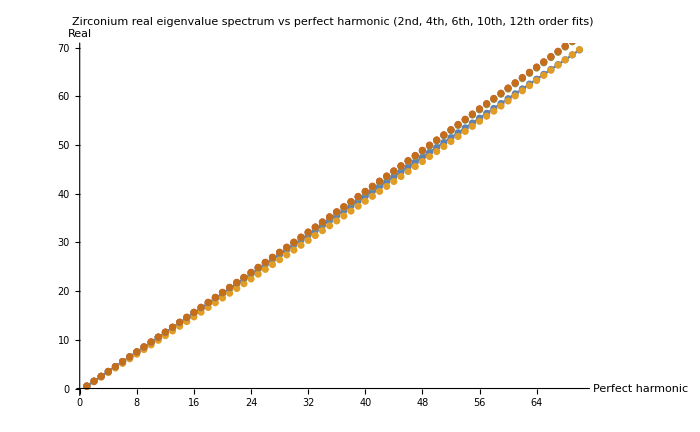

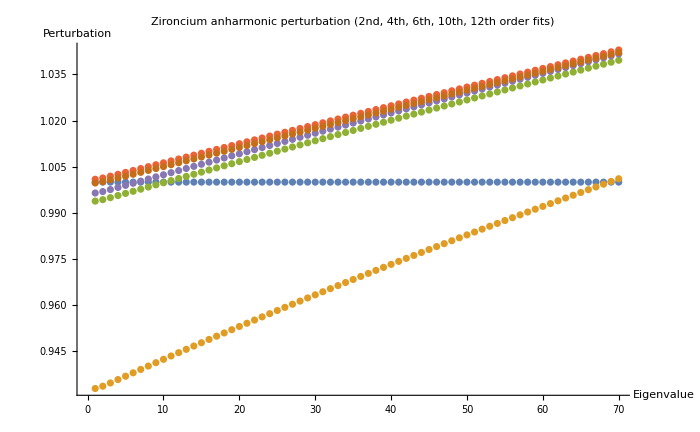

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5 | 68.5 | 69.5
0.466454 | 1.40049 | 2.33679 | 3.27532 | 4.21608 | 5.15905 | 6.10421 | 7.05155 | 8.00107 | 8.95273 | 9.90654 | 10.8625 | 11.8205 | 12.7807 | 13.7429 | 14.7072 | 15.6736 | 16.642 | 17.6125 | 18.585 | 19.5595 | 20.536 | 21.5145 | 22.495 | 23.4775 | 24.4619 | 25.4482 | 26.4366 | 27.4268 | 28.419 | 29.413 | 30.409 | 31.4068 | 32.4066 | 33.4082 | 34.4117 | 35.417 | 36.4241 | 37.4331 | 38.4439 | 39.4566 | 40.471 | 41.4873 | 42.5053 | 43.5251 | 44.5467 | 45.57 | 46.5951 | 47.622 | 48.6506 | 49.6809 | 50.7129 | 51.7467 | 52.7822 | 53.8194 | 54.8583 | 55.8988 | 56.9411 | 57.985 | 59.0306 | 60.0778 | 61.1267 | 62.1773 | 63.2295 | 64.2833 | 65.3387 | 66.3958 | 67.4545 | 68.5147 | 69.5766
0.496916 | 1.49145 | 2.48739 | 3.48474 | 4.48348 | 5.48361 | 6.48514 | 7.48805 | 8.49235 | 9.49803 | 10.5051 | 11.5135 | 12.5233 | 13.5345 | 14.547 | 15.5609 | 16.5762 | 17.5928 | 18.6108 | 19.6301 | 20.6507 | 21.6727 | 22.6961 | 23.7208 | 24.7468 | 25.7741 | 26.8028 | 27.8328 | 28.8641 | 29.8967 | 30.9307 | 31.966 | 33.0025 | 34.0404 | 35.0796 | 36.1201 | 37.1619 | 38.205 | 39.2494 | 40.2951 | 41.342 | 42.3903 | 43.4398 | 44.4907 | 45.5428 | 46.5961 | 47.6508 | 48.7067 | 49.7639 | 50.8223 | 51.882 | 52.943 | 54.0052 | 55.0687 | 56.1334 | 57.1994 | 58.2666 | 59.3351 | 60.4048 | 61.4758 | 62.548 | 63.6214 | 64.6961 | 65.772 | 66.8491 | 67.9275 | 69.007 | 70.0878 | 71.1699 | 72.2531
0.500464 | 1.50202 | 2.50484 | 3.5089 | 4.51423 | 5.5208 | 6.52863 | 7.5377 | 8.54803 | 9.5596 | 10.5724 | 11.5865 | 12.6018 | 13.6183 | 14.6361 | 15.6552 | 16.6754 | 17.6969 | 18.7197 | 19.7436 | 20.7689 | 21.7953 | 22.823 | 23.8519 | 24.882 | 25.9133 | 26.9459 | 27.9797 | 29.0147 | 30.051 | 31.0885 | 32.1271 | 33.167 | 34.2081 | 35.2505 | 36.294 | 37.3388 | 38.3847 | 39.4319 | 40.4803 | 41.5298 | 42.5806 | 43.6326 | 44.6858 | 45.7402 | 46.7958 | 47.8526 | 48.9106 | 49.9697 | 51.0301 | 52.0917 | 53.1544 | 54.2184 | 55.2835 | 56.3498 | 57.4173 | 58.486 | 59.5558 | 60.6269 | 61.6991 | 62.7725 | 63.8471 | 64.9228 | 65.9997 | 67.0778 | 68.1571 | 69.2375 | 70.3191 | 71.4019 | 72.4859
0.49823 | 1.49539 | 2.49395 | 3.4939 | 4.49525 | 5.49798 | 6.50209 | 7.50758 | 8.51444 | 9.52268 | 10.5323 | 11.5432 | 12.5556 | 13.5692 | 14.5843 | 15.6006 | 16.6183 | 17.6374 | 18.6578 | 19.6795 | 20.7026 | 21.7269 | 22.7526 | 23.7796 | 24.808 | 25.8376 | 26.8686 | 27.9008 | 28.9344 | 29.9692 | 31.0054 | 32.0428 | 33.0816 | 34.1216 | 35.1629 | 36.2055 | 37.2493 | 38.2945 | 39.3409 | 40.3885 | 41.4375 | 42.4877 | 43.5391 | 44.5918 | 45.6458 | 46.701 | 47.7575 | 48.8152 | 49.8741 | 50.9343 | 51.9957 | 53.0584 | 54.1223 | 55.1874 | 56.2538 | 57.3213 | 58.3901 | 59.4602 | 60.5314 | 61.6038 | 62.6775 | 63.7524 | 64.8284 | 65.9057 | 66.9842 | 68.0639 | 69.1448 | 70.2268 | 71.3101 | 72.3946
0.499859 | 1.5002 | 2.50179 | 3.50463 | 4.50872 | 5.51406 | 6.52065 | 7.52848 | 8.53757 | 9.5479 | 10.5595 | 11.5723 | 12.5864 | 13.6017 | 14.6183 | 15.6361 | 16.6552 | 17.6755 | 18.697 | 19.7198 | 20.7439 | 21.7692 | 22.7957 | 23.8235 | 24.8525 | 25.8827 | 26.9142 | 27.9469 | 28.9809 | 30.0161 | 31.0525 | 32.0902 | 33.1291 | 34.1693 | 35.2106 | 36.2532 | 37.2971 | 38.3421 | 39.3884 | 40.4359 | 41.4847 | 42.5346 | 43.5858 | 44.6382 | 45.6918 | 46.7467 | 47.8027 | 48.86 | 49.9185 | 50.9782 | 52.0391 | 53.1013 | 54.1646 | 55.2292 | 56.2949 | 57.3619 | 58.43 | 59.4994 | 60.57 | 61.6417 | 62.7147 | 63.7889 | 64.8642 | 65.9408 | 67.0185 | 68.0975 | 69.1776 | 70.2589 | 71.3414 | 72.4251

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.932907 | 0.933662 | 0.934714 | 0.935806 | 0.936906 | 0.938008 | 0.939109 | 0.940207 | 0.941302 | 0.942393 | 0.94348 | 0.944563 | 0.945642 | 0.946716 | 0.947786 | 0.948853 | 0.949915 | 0.950972 | 0.952026 | 0.953076 | 0.954121 | 0.955163 | 0.9562 | 0.957234 | 0.958263 | 0.959289 | 0.960311 | 0.961329 | 0.962344 | 0.963354 | 0.964361 | 0.965365 | 0.966364 | 0.96736 | 0.968353 | 0.969342 | 0.970328 | 0.97131 | 0.972289 | 0.973264 | 0.974236 | 0.975205 | 0.97617 | 0.977133 | 0.978092 | 0.979047 | 0.98 | 0.98095 | 0.981896 | 0.982839 | 0.98378 | 0.984717 | 0.985651 | 0.986583 | 0.987511 | 0.988437 | 0.989359 | 0.990279 | 0.991196 | 0.99211 | 0.993021 | 0.99393 | 0.994836 | 0.995739 | 0.996639 | 0.997537 | 0.998432 | 0.999325 | 1.00021 | 1.0011
0.993833 | 0.994302 | 0.994957 | 0.995639 | 0.996328 | 0.99702 | 0.997713 | 0.998407 | 0.9991 | 0.999792 | 1.00048 | 1.00118 | 1.00187 | 1.00255 | 1.00324 | 1.00393 | 1.00462 | 1.0053 | 1.00599 | 1.00667 | 1.00735 | 1.00803 | 1.00871 | 1.00939 | 1.01007 | 1.01075 | 1.01143 | 1.0121 | 1.01278 | 1.01345 | 1.01412 | 1.01479 | 1.01546 | 1.01613 | 1.0168 | 1.01747 | 1.01813 | 1.0188 | 1.01946 | 1.02013 | 1.02079 | 1.02145 | 1.02211 | 1.02277 | 1.02343 | 1.02409 | 1.02475 | 1.0254 | 1.02606 | 1.02671 | 1.02737 | 1.02802 | 1.02867 | 1.02932 | 1.02997 | 1.03062 | 1.03127 | 1.03191 | 1.03256 | 1.03321 | 1.03385 | 1.03449 | 1.03514 | 1.03578 | 1.03642 | 1.03706 | 1.0377 | 1.03834 | 1.03898 | 1.03961
1.00093 | 1.00135 | 1.00193 | 1.00254 | 1.00316 | 1.00378 | 1.0044 | 1.00503 | 1.00565 | 1.00627 | 1.0069 | 1.00752 | 1.00814 | 1.00877 | 1.00939 | 1.01001 | 1.01063 | 1.01125 | 1.01187 | 1.01249 | 1.01311 | 1.01373 | 1.01435 | 1.01497 | 1.01559 | 1.01621 | 1.01683 | 1.01744 | 1.01806 | 1.01868 | 1.01929 | 1.01991 | 1.02052 | 1.02114 | 1.02175 | 1.02237 | 1.02298 | 1.02359 | 1.0242 | 1.02482 | 1.02543 | 1.02604 | 1.02665 | 1.02726 | 1.02787 | 1.02848 | 1.02909 | 1.0297 | 1.0303 | 1.03091 | 1.03152 | 1.03212 | 1.03273 | 1.03334 | 1.03394 | 1.03455 | 1.03515 | 1.03575 | 1.03636 | 1.03696 | 1.03756 | 1.03816 | 1.03876 | 1.03937 | 1.03997 | 1.04057 | 1.04117 | 1.04176 | 1.04236 | 1.04296
0.99646 | 0.996927 | 0.99758 | 0.998258 | 0.998944 | 0.999632 | 1.00032 | 1.00101 | 1.0017 | 1.00239 | 1.00307 | 1.00376 | 1.00444 | 1.00513 | 1.00581 | 1.00649 | 1.00717 | 1.00785 | 1.00853 | 1.00921 | 1.00988 | 1.01056 | 1.01123 | 1.0119 | 1.01257 | 1.01324 | 1.01391 | 1.01458 | 1.01524 | 1.01591 | 1.01657 | 1.01723 | 1.01789 | 1.01855 | 1.01921 | 1.01987 | 1.02053 | 1.02119 | 1.02184 | 1.02249 | 1.02315 | 1.0238 | 1.02445 | 1.0251 | 1.02575 | 1.0264 | 1.02704 | 1.02769 | 1.02833 | 1.02898 | 1.02962 | 1.03026 | 1.0309 | 1.03154 | 1.03218 | 1.03282 | 1.03345 | 1.03409 | 1.03472 | 1.03536 | 1.03599 | 1.03662 | 1.03725 | 1.03788 | 1.03851 | 1.03914 | 1.03977 | 1.0404 | 1.04102 | 1.04165
0.999719 | 1.00013 | 1.00072 | 1.00132 | 1.00194 | 1.00256 | 1.00318 | 1.0038 | 1.00442 | 1.00504 | 1.00567 | 1.00629 | 1.00691 | 1.00753 | 1.00816 | 1.00878 | 1.0094 | 1.01003 | 1.01065 | 1.01127 | 1.0119 | 1.01252 | 1.01314 | 1.01376 | 1.01439 | 1.01501 | 1.01563 | 1.01625 | 1.01687 | 1.01749 | 1.01812 | 1.01874 | 1.01936 | 1.01998 | 1.0206 | 1.02122 | 1.02184 | 1.02246 | 1.02308 | 1.02369 | 1.02431 | 1.02493 | 1.02555 | 1.02617 | 1.02678 | 1.0274 | 1.02802 | 1.02863 | 1.02925 | 1.02986 | 1.03048 | 1.03109 | 1.03171 | 1.03232 | 1.03293 | 1.03355 | 1.03416 | 1.03477 | 1.03538 | 1.036 | 1.03661 | 1.03722 | 1.03783 | 1.03844 | 1.03905 | 1.03966 | 1.04026 | 1.04087 | 1.04148 | 1.04209

```mathematica
Zirconium - look at harmonic and anharmonic eigenvalues;
(*zOmega=13.44788050977517;M=91;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)

Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues},PlotLabel->"Zirconium real eigenvalue spectrum vs perfect harmonic \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Perfect harmonic","Real"}],ListPlot@eigenEnergiesZ,ImageSize->700]
relativeEigenvalz=Table[eigensysZ[[k]][[1]]/eigensysZ[[1]][[1]],{k,1,6}];
Show[ListPlot[relativeEigenvalz,ImageSize->700,PlotLabel->"Zironcium anharmonic perturbation \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Eigenvalue","Perturbation"}]]

eigenEnergiesZ//TableForm
relativeEigenvalz//TableForm
```

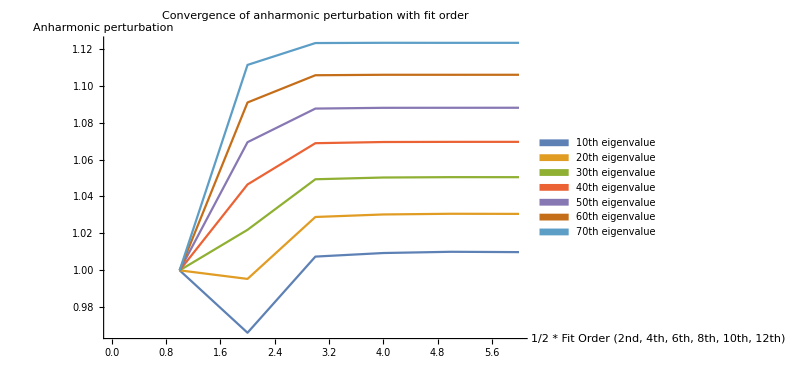

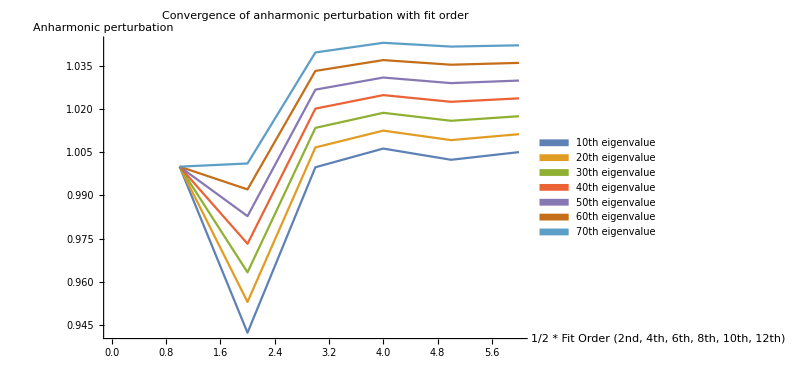

```mathematica
Carbon and zirconium - check convergence of eigenvalues with fit order;
plotstuff={ImageSize->600,PlotLegends->SwatchLegend[{"10th eigenvalue","20th eigenvalue","30th eigenvalue","40th eigenvalue","50th eigenvalue","60th eigenvalue","70th eigenvalue"}],PlotLabel->"Convergence of anharmonic perturbation with fit order",AxesLabel->{"1/2 * Fit Order \n(2nd, 4th, 6th, 8th, 10th, 12th)","Anharmonic\nperturbation"}};
ListPlot[Table[Transpose[relativeEigenval][[i]],{i,10,70,10}], Joined->True,plotstuff]
ListPlot[Table[Transpose[relativeEigenvalz][[i]],{i,10,70,10}], Joined->True,plotstuff]
```

```mathematica
Plot input stuff for Carbon eigensystem;
(*eigenPlots=Table[Show[Plot[Evaluate[(6*eigensysC[[i]][[2]])+eigensysC[[i]][[1]]],{x,-B,B}],Plot[Evaluate@V[1,2i,x],{x,-B,B}],PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};*)
```

```mathematica
Plot carbon potential and eigensystem (eigenvectors and eigenvectors*eigenvalues);
(*GraphicsGrid[plotgrid,ImageSize->1100]*)
```

```mathematica
Plot input stuff for Zr eigensystem;
(*Bz=0.5;Hz=1000;
eigenPlotsz=Table[Show[Plot[Evaluate[(4*eigensysZ[[i]][[2]])+eigensysZ[[i]][[1]]],{x,-Bz,Bz}],Plot[Evaluate@V[2,2i,x],{x,-Bz,Bz}],PlotRange->{{-Bz,Bz},{0,Hz}},AxesOrigin->{-Bz,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};
plotgridz={Table[eigenPlotsz[[i]],{i,1,2}],Table[eigenPlotsz[[j]],{j,3,4}],Table[eigenPlotsz[[k]],{k,5,6}]};*)
```

```mathematica
Plot zirconium eigensystem;
(*GraphicsGrid[plotgridz,ImageSize->1100]*)
```

0.991803+0.00191269 x

0.989006+0.00214581 x-3.28336×10^-6 x^2

0.988968+0.00215205 x-3.50165×10^-6 x^2+2.04967×10^-9 x^3

0.989124+0.00211056 x-9.15205×10^-7 x^2-5.43463×10^-8 x^3+3.97155×10^-10 x^4

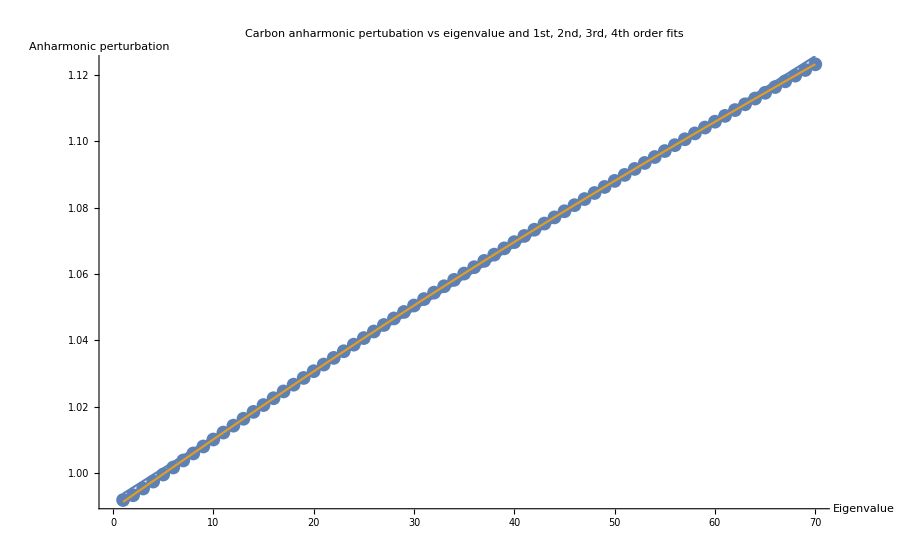

```mathematica
Carbon - fit an approximate analytic function to the anharmonic perturbation;
(*Make a function of different polynomial orders*)
anharmonicfit1=Fit[relativeEigenval[[5]],{1,x},x]
anharmonicfit2=Fit[relativeEigenval[[5]],{1, x, x^2},x]
anharmonicfit3=Fit[relativeEigenval[[5]],{1, x, x^2,x^3},x]
anharmonicfit4=Fit[relativeEigenval[[5]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenval[[5]],PlotLabel->"Carbon anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ImageSize->900]
```

Null Zirconium

0.998913+0.000618266 x

0.998837+0.000624629 x-8.96123×10^-8 x^2

0.998903+0.000613919 x+2.8482×10^-7 x^2-3.5158×10^-9 x^3

0.998953+0.000600564 x+1.11733×10^-6 x^2-2.16683×10^-8 x^3+1.27834×10^-10 x^4

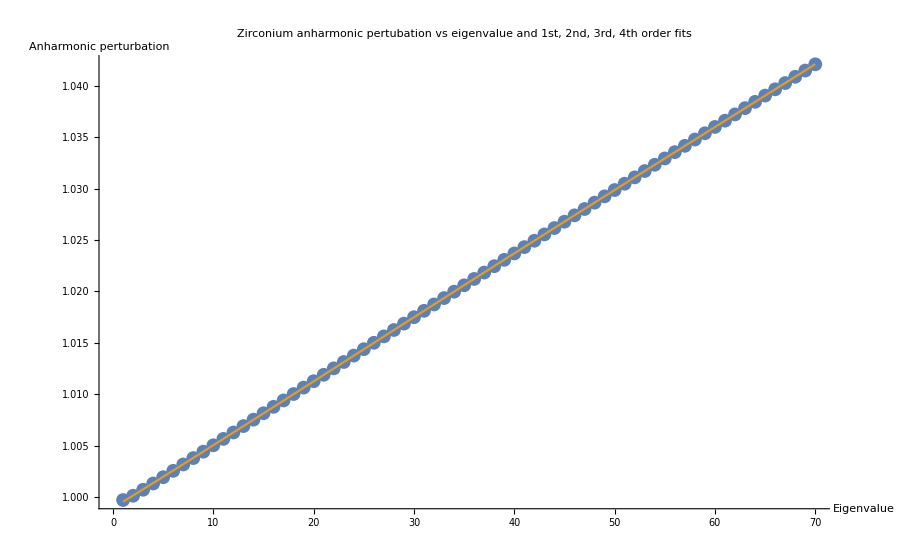

```mathematica
Zirconium - fit an approximate analytic function to the anharmonic perturbation;
(*Make a function of different polynomial orders*)
anharmonicfit1z=Fit[relativeEigenvalz[[6]],{1,x},x]
anharmonicfit2z=Fit[relativeEigenvalz[[6]],{1, x, x^2},x]
anharmonicfit3z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3},x]
anharmonicfit4z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenvalz[[6]],PlotLabel->"Zirconium anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

0.998535+0.00060755 x+1.13021×10^-6 x^2-2.19648×10^-8 x^3+1.29516×10^-10 x^4

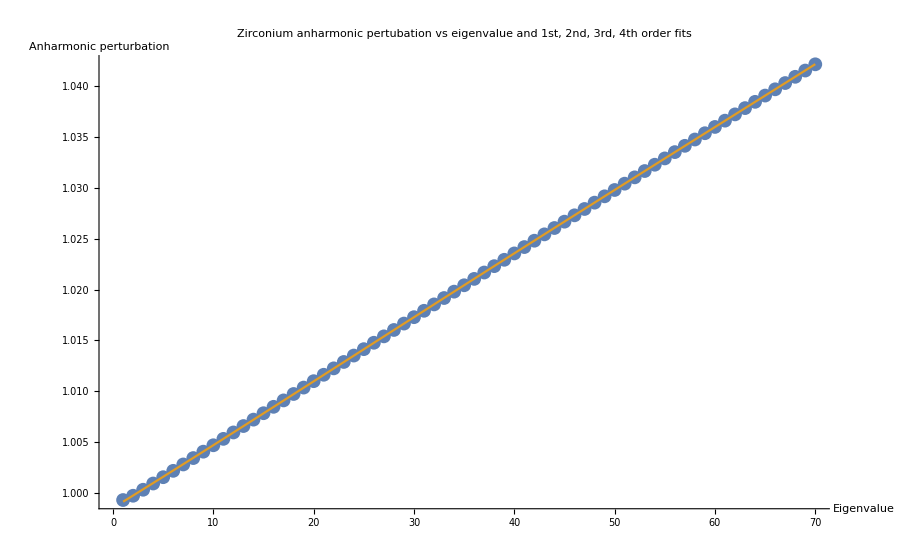

```mathematica
0.9984840779371645+0.0006210804635938045 x+2.867500483226181*^-7 x^2-3.573477223788385*^-9 x^3
```

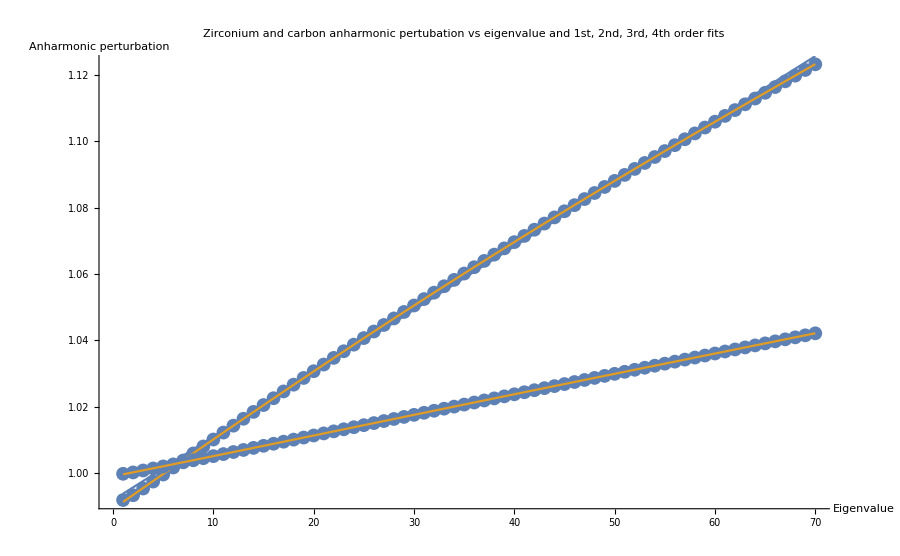

```mathematica
(*Compare C and Zr anharmonic perturbations*)
Show[ListPlot[relativeEigenval[[5]],PlotLabel->"Zirconium and carbon anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ListPlot[relativeEigenvalz[[6]]],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

```mathematica
(*Plot derivitive of C and Zr anharmonic perturbation fits*)
(*cAnharmonicityDerivitive=D[{anharmonicfit1,anharmonicfit2,anharmonicfit3,anharmonicfit4},x]
zrAnharmonicityDerivitive=D[{anharmonicfit1z,anharmonicfit2z,anharmonicfit3z,anharmonicfit4z},x]
GraphicsGrid[{{Show@Plot[{cAnharmonicityDerivitive},{x,0,70},ImageSize->400],Show@Plot[{zrAnharmonicityDerivitive},{x,0,70}]}}]*)
```

```mathematica
(*Calculate partition function and Helmholtz free energy with Einstein frequencies*)
(*As previous, define omega0 as the solution to A*x*x=1/2*m*omega*omega*x*x, where A*x*x is the harmonic fit*)
"4.685Ang Einstein frequencies from polynomial fit:"
Acarbon=V[1,2,X][[1]];
cOmega0=Sqrt[2Acarbon/m[[1]]]
Azirconium=V[2,2,X][[1]];
zOmega0=Sqrt[2Azirconium/m[[2]]] 
(*Note, if we define the Einstein frequency in terms of the QHA DOS as the energy integrating up to which gives the number of modes equal to the 3*Natoms/2, then the frequencies are*)
"4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:"
cOmegaInt48=65.1879672429008/2
zrOmegaInt48=26.329538754361874/2
"4.685Ang Einstein frequencies from QHA finding peak frequency for each band:"
cOmegaMaxPeak=4.14*18.0295229515/2
zrOmegaMaxPeak=4.14*6.2446881878/2
```

4.685Ang Einstein frequencies from polynomial fit:

28.8486

11.8968

4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:

32.594

13.1648

4.685Ang Einstein frequencies from QHA finding peak frequency for each band:

37.3211

12.9265

```mathematica
(*Zirconium eigenspectrum*)
(*Ideal harmonic eigenvalue spectrum*)
perfectHarmonic=Table[0.5+i,{i,0,69}];
Partition[perfectHarmonic,15]//TableForm
(*2nd order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergiesZ[[1]],15]//TableForm
(*12th order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergiesZ[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.499859 | 1.5002 | 2.50179 | 3.50463 | 4.50872 | 5.51406 | 6.52065 | 7.52848 | 8.53757 | 9.5479 | 10.5595 | 11.5723 | 12.5864 | 13.6017 | 14.6183
15.6361 | 16.6552 | 17.6755 | 18.697 | 19.7198 | 20.7439 | 21.7692 | 22.7957 | 23.8235 | 24.8525 | 25.8827 | 26.9142 | 27.9469 | 28.9809 | 30.0161
31.0525 | 32.0902 | 33.1291 | 34.1693 | 35.2106 | 36.2532 | 37.2971 | 38.3421 | 39.3884 | 40.4359 | 41.4847 | 42.5346 | 43.5858 | 44.6382 | 45.6918
46.7467 | 47.8027 | 48.86 | 49.9185 | 50.9782 | 52.0391 | 53.1013 | 54.1646 | 55.2292 | 56.2949 | 57.3619 | 58.43 | 59.4994 | 60.57 | 61.6417

```mathematica
(*Carbon eigenspectrum*)
(*Ideal harmonic eigenvalue spectrum*)
perfectHarmonic=Table[0.5+i,{i,0,69}];
Partition[perfectHarmonic,15]//TableForm
(*2nd order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergies[[1]],15]//TableForm
(*12th order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergies[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.495719 | 1.48936 | 2.48739 | 3.48977 | 4.49648 | 5.50747 | 6.52274 | 7.54223 | 8.56593 | 9.5938 | 10.6258 | 11.662 | 12.7022 | 13.7465 | 14.7948
15.8472 | 16.9036 | 17.9639 | 19.0281 | 20.0963 | 21.1684 | 22.2443 | 23.3241 | 24.4077 | 25.4951 | 26.5863 | 27.6813 | 28.78 | 29.8824 | 30.9885
32.0983 | 33.2118 | 34.3289 | 35.4496 | 36.5739 | 37.7018 | 38.8333 | 39.9683 | 41.1069 | 42.2489 | 43.3945 | 44.5435 | 45.696 | 46.8519 | 48.0113
49.174 | 50.3402 | 51.5097 | 52.6826 | 53.8588 | 55.0384 | 56.2213 | 57.4074 | 58.5969 | 59.7896 | 60.9856 | 62.1849 | 63.3873 | 64.593 | 65.8019

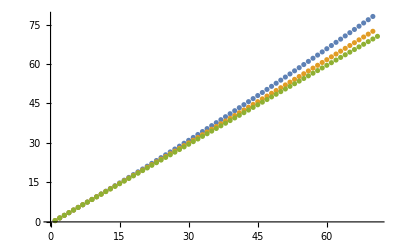

```mathematica
ListPlot[{eigenEnergies[[6]],eigenEnergiesZ[[6]],Table[i+1/2,{i,0,70}]}]
```

```mathematica
(*Define standard harmonic omega argument thermodynamic functions - Helmholtz - entropy - Cv*)
K2meV=0.086173324;
HH[T_,Einsteinlist_]:=1.5*(0.5*Total[Einsteinlist]+K2meV*T*Total[Log[1-Exp[-((Einsteinlist)/(K2meV*T))]]])

SS[T_,Einsteinlist_]:=1.5*((1/(2*T))*Total[Einsteinlist*Coth[(Einsteinlist)/(2*K2meV*T)]]-K2meV*Total[Log[2*Sinh[(Einsteinlist)/(2*K2meV*T)]]])

EE[T_,Einsteinlist_]:=1.5*(Total[(Einsteinlist)/2]+Total[1/(Exp[Einsteinlist/(K2meV*T)]-1)])

CC[T_,Einsteinlist_]:=1.5*Total[K2meV*(((Einsteinlist)/(K2meV*T))^2)*(Exp[Einsteinlist/(K2meV*T)]/((Exp[Einsteinlist/(K2meV*T)]-1)^2))]
```

```mathematica
(*Zero point energies*)
(*QHA 48 mode Einstein oscillators*)
zpeEinstein=HH[0.00001,Einstein4685]
(*QHA *)
zpeQHA4685=thermalData4685[[6]][[1]]
(*Quadratic fit to harmonic Einstein oscillator potential for 4.685*)
1.5*(zOmega0+cOmega0)
```

Total::normal: Nonatomic expression expected at position 1 in Total[Einstein4685].

1.5 (8.61733×10^-7 (1-ⅇ^(-1.16045×10^6 Einstein4685))+0.5 Total[Einstein4685])

Part::partd: Part specification thermalData4685⟦6⟧ is longer than depth of object.

thermalData4685

61.1182

```mathematica
Define a more general partition that takes as argument an arbitary eigenspectrum;
(*Partition function as a power series expansion of eigenspectrum http://www.nyu.edu/classes/tuckerman/stat.mech/lectures/lecture_13/node8.html *)
Zpower[T_,eigenlist_]:=Exp[-eigenlist/(2*K2meV*T)]*Total[Table[Exp[-eigenlist/(K2meV*T)]^k,{k,0,100}]]
Zgen[T_,order_]:={Total[Exp[-2*zOmega0*eigenEnergiesZ[[order]]/(K2meV*T)]],Total[Exp[-2*cOmega0*eigenEnergies[[order]]/(K2meV*T)]]}
```

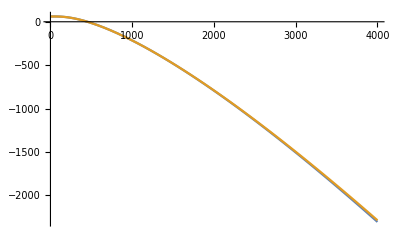

```mathematica
Define free energy of Helmholtz via partition function;
einsteinOmega0=2{zOmega0,cOmega0};
maxEigen=100;
Apower[T_,eigenlist_]:=-K2meV*1.5T*Log[Zpower[T,eigenlist]]
A[T_,1]:=-K2meV*1.5*T*Log[Zgen[T,1]]
A[T_,6]:=-K2meV*1.5*T*Log[Zgen[T,6]]
(*Perfect Einstein Helmholtz Free energy from partition function*)
Define free energy via partition function;
Plot[{Total@Apower[T,einsteinOmega0],Total@A[T,6]},{T,1,4000}]
```

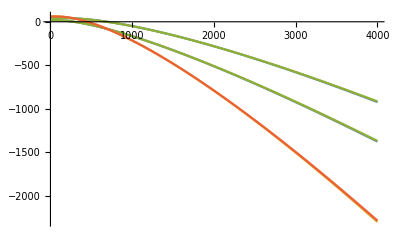

```mathematica
Plot[{{A[T,1],Total@A[T,1]},{A[T,6],Total@A[T,6]}},{T,1,4000}]
```

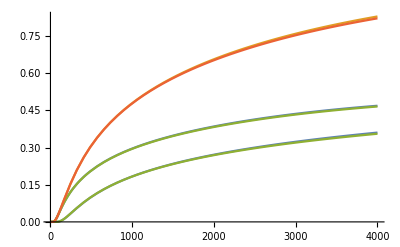

-Graphics-

```mathematica
Define entropy via partition function;
S[T_,order_]:=-D[A[t,order],t]/.t->T
Plot[{{-D[A[t,1],t]/.t->T,Total@-D[A[t,1],t]/.t->T},{-D[A[t,6],t]/.t->T,Total@-D[A[t,6],t]/.t->T}},{T,1,4000}]
Plot[{{S[T,1],Total@S[T,1]},{S[T,6],Total@S[T,6]}},{T,1,4000}]
```

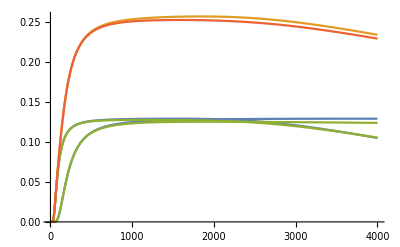

-Graphics-

```mathematica
Define heat capacity via partition function;
Plot[{{-t*D[D[A[t,1],t],t]/.t->T,Total[-t*D[D[A[t,1],t],t]]/.t->T},{-t*D[D[A[t,6],t],t]/.t->T,Total[-t*D[D[A[t,6],t],t]]/.t->T}},{T,1,4000}]

Heat[T_,order_]:=t*D[S[t,order],t]/.t->T
Plot[{{Heat[T,1],Total[Heat[T,1]]},{Heat[T,6],Total[Heat[T,6]]}},{T,1,4000}]
```

```mathematica
spectrumAnharmonicZ= Table[0.5+x*anharmonicfit4z,{x,0,1000}];
spectrumAnharmonicC=Table[0.5+x*anharmonicfit4,{x,0,1000}];
ZanharmonicFit[T_,spectrumZ_,spectrumC_]:={Total[Exp[-2*zOmega0*spectrumZ/(K2meV*T)]],Total[Exp[-2*cOmega0*spectrumC/(K2meV*T)]]}
ZanharmonicFit[T,spectrumAnharmonicZ,spectrumAnharmonicC];
Afit[T_]:=-K2meV*1.5*T*Log[ZanharmonicFit[T,spectrumAnharmonicZ,spectrumAnharmonicC]]
```

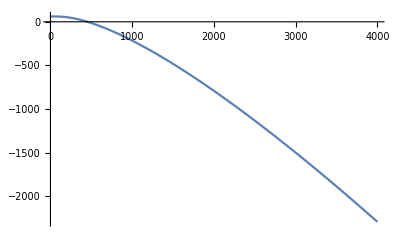

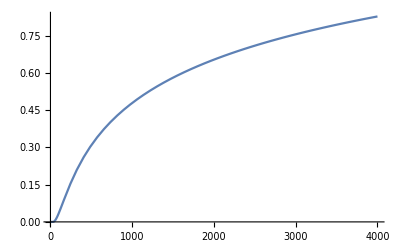

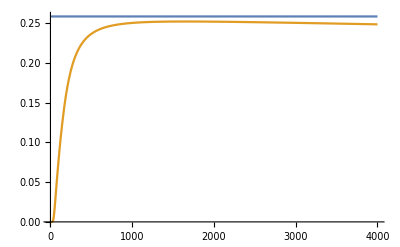

```mathematica
Plot[{Total@Afit[T]},{T,1,4000}]
Plot[{Total@-D[Afit[T],T]/.T->t},{t,1,4000}]
Plot[{K2meV*3,Total[T*D[-D[Afit[T],T],T]]/.T->t},{t,1,4000},PlotRange->All]
```

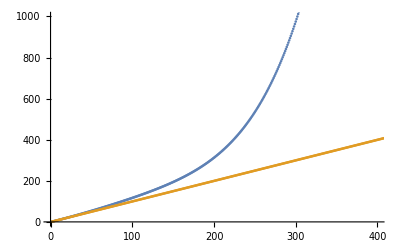

```mathematica
ListPlot[{spectrumAnharmonicC,Table[0.5+i,{i,0,1000}]},PlotRange->{{0,400},{0,1000}}]
```